```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{120,267}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20,4/26/20,4/27/20,4/28/20,4/29/20,4/30/20,5/1/20,5/2/20,5/3/20,5/4/20,5/5/20,5/6/20,5/7/20,5/8/20,5/9/20,5/10/20,5/11/20,5/12/20,5/13/20,5/14/20,5/15/20,5/16/20,5/17/20}

117

{267}

```mathematica
TableForm[series];
```

```mathematica
TableForm[s];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Spain",300,{220179.72743729973,3738.260142762334,0.140854450046756},35,21,3,0},{"Canada",200,{81077.39354813701,1942.4785517808518,0.09614986026664779},21,21,10,0},{"Australia",100,{6739.694777539763,109.80989304529129,0.2176890747257849},35,21,3,0},{"New Zealand",5,{1474.4790552718507,17.837297202136803,0.22787919159710443},21,21,10,0},{"Croatia",10,{2136.3445533928943,31.72191300732455,0.14074152304198262},42,21,2,0},{"Czechia",10,{7901.635972368201,127.858460333728,0.13557437401035852},28,21,5,0},{"Sweden",200,{31272.793301689162,709.071763360148,0.08355406779130738},28,21,10,0},{"Greece",50,{2666.2946598125536,129.93576587902731,0.11994181591439824},28,21,10,0},{"Japan",950,{16302.099406766767,451.80679351636303,0.1327048660761382},28,21,8,0},{"Denmark",1100,{10976.989187588755,1103.472360444931,0.09290172311994832},28,21,10,0},{"Russia",300,{369442.4708046471,1404.1124969291448,0.114562446419243},21,21,10,0},{"United Kingdom",200,{242613.6018213363,2637.774825046479,0.10113748577252618},21,14,10,0},{"Hungary",50,{3497.602134723886,112.69091970270172,0.10969692792738958},35,21,5,0},{"France",300,{177843.2636752088,1554.9147679208638,0.1371138414227038},35,21,5,0},{"Singapore",900,{26421.784728354156,555.472525673107,0.1403556555382898},28,21,5,0},{"Serbia",50,{10410.396290570648,127.16306680915262,0.13621047340777273},28,21,5,0},{"Poland",50,{17709.029565845885,459.31825489863706,0.09649995071438171},35,21,5,0}
}
```

{{Spain,300,{220180.,3738.26,0.140854},35,21,3,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},35,21,3,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},42,21,2,0},{Czechia,10,{7901.64,127.858,0.135574},28,21,5,0},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},35,21,5,0},{France,300,{177843.,1554.91,0.137114},35,21,5,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},28,21,5,0},{Poland,50,{17709.,459.318,0.0965},35,21,5,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{220180.,3738.26,0.140854},35,21,3,0},{Canada,200,{81077.4,1942.48,0.0961499},21,21,10,0},{Australia,100,{6739.69,109.81,0.217689},35,21,3,0},{New Zealand,5,{1474.48,17.8373,0.227879},21,21,10,0},{Croatia,10,{2136.34,31.7219,0.140742},35,21,3,0},{Czechia,10,{7901.64,127.858,0.135574},21,21,10,0},{Sweden,200,{31272.8,709.072,0.0835541},28,21,10,0},{Greece,50,{2666.29,129.936,0.119942},28,21,10,0},{Japan,950,{16302.1,451.807,0.132705},28,21,8,0},{Denmark,1100,{10977.,1103.47,0.0929017},28,21,10,0},{Russia,300,{369442.,1404.11,0.114562},21,21,10,0},{United Kingdom,200,{242614.,2637.77,0.101137},21,14,10,0},{Hungary,50,{3497.6,112.691,0.109697},28,21,10,0},{France,300,{177843.,1554.91,0.137114},28,21,10,0},{Singapore,900,{26421.8,555.473,0.140356},28,21,5,0},{Serbia,50,{10410.4,127.163,0.13621},28,21,5,0},{Poland,50,{17709.,459.318,0.0965},21,21,5,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Spain","Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark","Russia","United Kingdom","Hungary","France","Singapore","Serbia","Poland"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
lesscountrynames={};
morecountrynames={};
countrybootabcs={};
lesscountrybootabcs={};
morecountrybootabcs={};
```

{47290504,35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958,142400066,63556184,9918377,64101308,5336859,7164132,38344752}

```mathematica
lesscountrybootabcs={};
morecountrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

(*jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];*)

Print[jdatestring];

If[jp20[[1]]10^5/wpopulations[[cit]]>grafthreshhold,
morecountrynames=AppendTo[morecountrynames,currentnamme],
lesscountrynames=AppendTo[lesscountrynames,currentnamme]
];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];
(*uk  string exception*)
If[currentnamme==="United Kingdom",currentnamme="uk"];


datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

country : Spain

data length : 73

start date : {2020,3,6}

Set::shape: Lists {jdp0, tp1, tp2, tp3} and GNiteration[{400, 500, 673, 1073, 1695, 2277, 2277, 5232, 6391, 7798, 9942, 11748, 13910, 17963, 20410, 25374, 28768, 35136, 39885, 49515, 57786, 65719, 73235, 80110, 87956, 95923, 104118, 112065, 119199, 126168, 131646, 136675, 141942, 148220, 153222, 158273, 163027, 166831, 170099, 172541, 177644, 184948, 190839, 191726, 198674, 200210, 204178, 208389, 213024, 202990, « 23 »}, « 1 », {1, 2, 3, 4, 5, « 41 », 47, 48, 49, 50, « 23 »}] are not the same shape.

jdp0 : {220180.,3738.26,0.140854}

Set::shape: Lists {jp20, jabctab, jwinds} and « 1 » are not the same shape.

jp20 : jp20

Set::shape: Lists {jgraf, jloggraf, jdfpplot, jprogplot, jfinal, jbootabc} and somegraphs2[{220180., 3738.26, 0.140854}, jp20, {1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, 23, 24, 25, 26, 27, 28, 29, 30, 31, 32, 33, 34, 35, 36, 37, 38, 39, 40, 41, 42, 43, 44, 45, 46, 47, 48, 49, 50, « 23 »}, « 4 », 5, 3, 47290504] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,6},72]

Part::partd: Part specification jp20 ⟦ 1 ⟧ is longer than depth of object.

Spaindate.txt

Spaingraf.png

Spainloggraf.png

Spaindfgraf.png

Spainfinalplot.png

country : Canada

data length : 64

start date : {2020,3,15}

jdp0 : {81077.4,1942.48,0.0961499}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,15},63]

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 69

start date : {2020,3,10}

jdp0 : {6739.69,109.81,0.217689}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,10},68]

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 65

start date : {2020,3,14}

jdp0 : {1474.48,17.8373,0.227879}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,14},64]

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 73

start date : {2020,3,6}

jdp0 : {2136.34,31.7219,0.140742}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,6},72]

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 74

start date : {2020,3,5}

jdp0 : {7901.64,127.858,0.135574}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,5},73]

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 71

start date : {2020,3,8}

jdp0 : {31272.8,709.072,0.0835541}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,8},70]

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 71

start date : {2020,3,8}

jdp0 : {2666.29,129.936,0.119942}

jp20 : jp20

jgraf

jloggraf

jfinal

reldatetostring[{2020,3,8},70]

Greecedate.txt

$Aborted

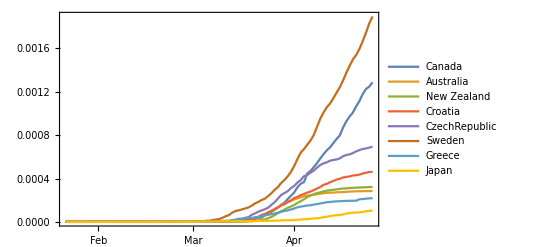

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

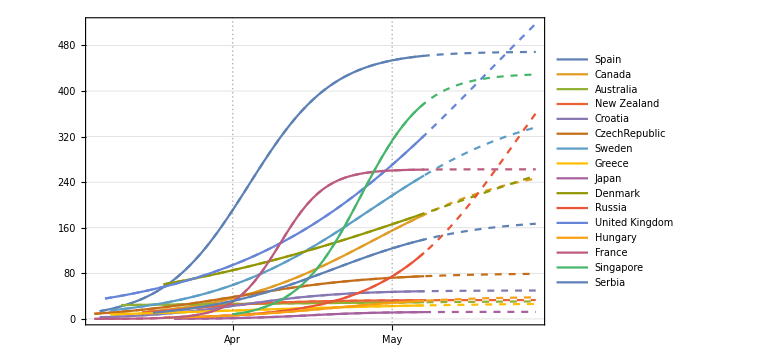

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

```mathematica
countrybootabcs//Length
morecountrybootabcs//Length
lesscountrybootabcs//Length
morecountrynames
lesscountrynames
```

17

9

8

{Spain,Canada,Sweden,Denmark,Russia,United Kingdom,France,Singapore,Serbia}

{Australia,New Zealand,Croatia,Czechia,Greece,Japan,Hungary,Poland}

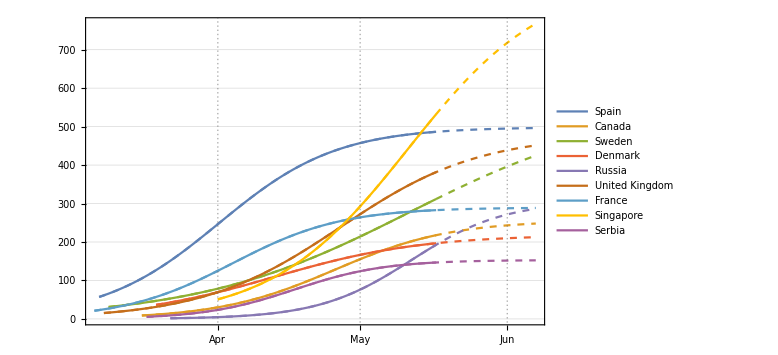

```mathematica
projfwcountryplot=DateListPlot[morecountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,morecountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->morecountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["moremscprojplots.png",mscprojplots]
```

moremscprojplots.png

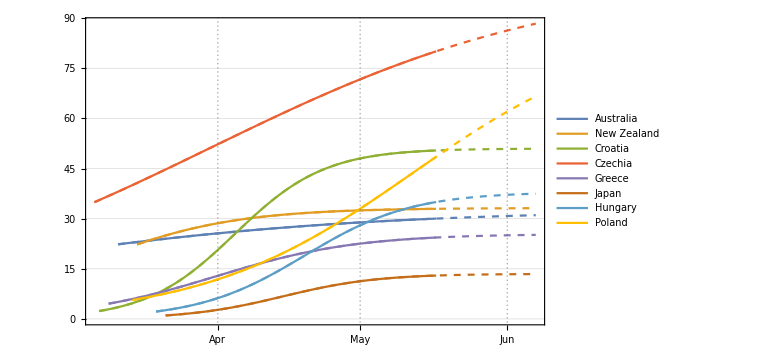

```mathematica
projfwcountryplot=DateListPlot[lesscountrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,lesscountrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->lesscountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

```mathematica
Export["lessmscprojplots.png",mscprojplots]
```

lessmscprojplots.png

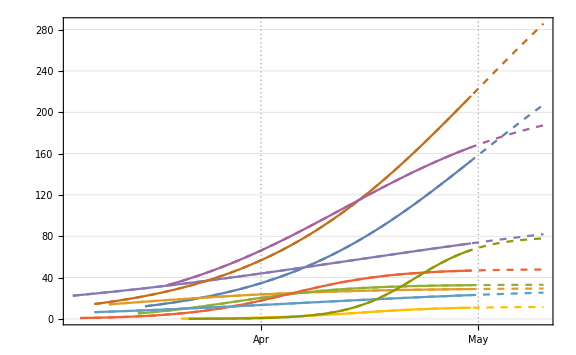
```mathematica
29.4.
-Graphics-
```

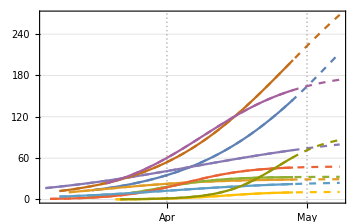
```mathematica
28.4.
-Graphics-
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

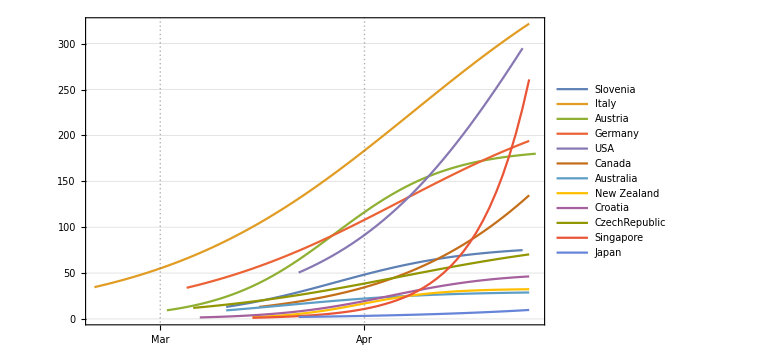

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"Poland"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{185}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},0},{{2020,2,1},0},{{2020,2,2},0},{{2020,2,3},0},{{2020,2,4},0},{{2020,2,5},0},{{2020,2,6},0},{{2020,2,7},0},{{2020,2,8},0},{{2020,2,9},0},{{2020,2,10},0},{{2020,2,11},0},{{2020,2,12},0},{{2020,2,13},0},{{2020,2,14},0},{{2020,2,15},0},{{2020,2,16},0},{{2020,2,17},0},{{2020,2,18},0},{{2020,2,19},0},{{2020,2,20},0},{{2020,2,21},0},{{2020,2,22},0},{{2020,2,23},0},{{2020,2,24},0},{{2020,2,25},0},{{2020,2,26},0},{{2020,2,27},0},{{2020,2,28},0},{{2020,2,29},0},{{2020,3,1},0},{{2020,3,2},0},{{2020,3,3},0},{{2020,3,4},1},{{2020,3,5},1},{{2020,3,6},5},{{2020,3,7},5},{{2020,3,8},11},{{2020,3,9},16},{{2020,3,10},22},{{2020,3,11},31},{{2020,3,12},49},{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>50&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,13},68},{{2020,3,14},103},{{2020,3,15},119},{{2020,3,16},177},{{2020,3,17},238},{{2020,3,18},251},{{2020,3,19},355},{{2020,3,20},425},{{2020,3,21},536},{{2020,3,22},634},{{2020,3,23},749},{{2020,3,24},901},{{2020,3,25},1051},{{2020,3,26},1221},{{2020,3,27},1389},{{2020,3,28},1638},{{2020,3,29},1862},{{2020,3,30},2055},{{2020,3,31},2311},{{2020,4,1},2554},{{2020,4,2},2946},{{2020,4,3},3383},{{2020,4,4},3627},{{2020,4,5},4102},{{2020,4,6},4413},{{2020,4,7},4848},{{2020,4,8},5205},{{2020,4,9},5575},{{2020,4,10},5955},{{2020,4,11},6356},{{2020,4,12},6674},{{2020,4,13},6934},{{2020,4,14},7202},{{2020,4,15},7582},{{2020,4,16},7918},{{2020,4,17},8379},{{2020,4,18},8742},{{2020,4,19},9287},{{2020,4,20},9593},{{2020,4,21},9856},{{2020,4,22},10169},{{2020,4,23},10511},{{2020,4,24},10892},{{2020,4,25},11273},{{2020,4,26},11617},{{2020,4,27},11902},{{2020,4,28},12218},{{2020,4,29},12640},{{2020,4,30},12877},{{2020,5,1},13105},{{2020,5,2},13375},{{2020,5,3},13693},{{2020,5,4},14006},{{2020,5,5},14431},{{2020,5,6},14740},{{2020,5,7},15047},{{2020,5,8},15366}}

57

{68,103,119,177,238,251,355,425,536,634,749,901,1051,1221,1389,1638,1862,2055,2311,2554,2946,3383,3627,4102,4413,4848,5205,5575,5955,6356,6674,6934,7202,7582,7918,8379,8742,9287,9593,9856,10169,10511,10892,11273,11617,11902,12218,12640,12877,13105,13375,13693,14006,14431,14740,15047,15366}

{2020,3,13}

```mathematica
jdp0={Max[justdata]1.5,150,0.12}
```

{23049.,150,0.12}

```mathematica
jdp0={2.835279843883035*^8,64.38918662693713,0.1259411788554341}
```

{2.83528×10^8,64.3892,0.125941}

```mathematica
jdp0={1.1513551375078703*^6,30102.77946079763,0.1242005827138709}
```

{1.15136×10^6,30102.8,0.124201}

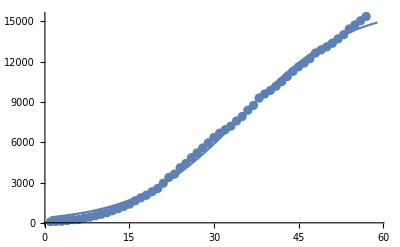

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{16098.4,370.628,0.106508},14,2.69826×10^-8,57}

{19509.6,978.105,0.0737384}

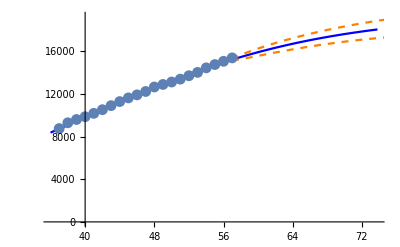
{-Graphics-,242.344,98.9939,319,-17.1075,78.7611}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,28,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0}
```

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

```mathematica
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
{"Hungary",50,{3365.6444625267736,104.40659882066325,0.11408451894205024},28,14,10,0}
{"France",50,{177276.3912847858,1518.766119969371,0.13797898997605668},28,14,10,0}
{"Singapore",900,{21078.466173566427,299.80354836134035,0.17802870984146776},28,14,5,0}
{"Serbia",50,{10139.282988917936,113.99752601777078,0.1410478828462318},21,14,10,0}
{"Poland",50,{16098.415437312473,370.62817701093553,0.1065084233501309},21,14,10,0}
```

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

last tab: {21779.4,1446.22,0.0613938}

backward result : {5109.3,89.9793,0.203261}

forward result : {21779.4,1446.22,0.0613938}

past errors : {{117.158,64.109,13.5794,16.8407,80.06,150.308,344.565,434.733,534.641,658.056},241.405}

boot tab : {{13627.2,229.936,0.131347},{11114.3,195.435,0.142952},{10824.6,192.529,0.144397},{10136.9,166.727,0.152786},{10413.6,178.982,0.14892},{10892.5,200.413,0.142841},{11475.1,232.693,0.1352},{13056.1,314.746,0.119793},{14215.8,393.753,0.109384},{15056.2,469.13,0.101855},{16576.3,584.856,0.0922481},{18811.3,722.096,0.0829107},{21650.4,856.053,0.0752707},{25305.2,1013.54,0.0680646},{28097.1,1131.12,0.063654},{28821.6,1227.54,0.0610384},{28616.2,1291.62,0.0596942},{28461.2,1361.97,0.0582909},{25710.5,1350.59,0.0598001},{23260.5,1284.86,0.0627113},{21267.1,1166.66,0.0670085},{20420.5,1097.63,0.0695436},{20210.8,1097.91,0.0698218},{20915.,1215.07,0.0664652},{21692.,1365.15,0.0627461},{23200.1,1614.66,0.0572315},{25449.5,1913.16,0.0514437}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57}

May 09

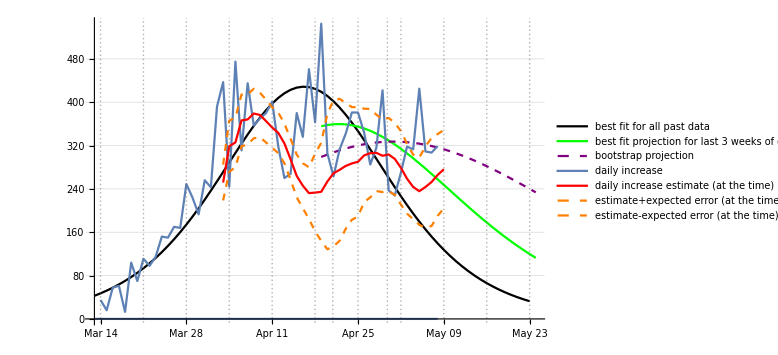

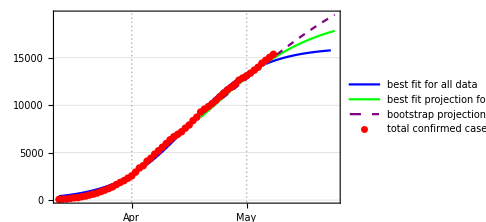

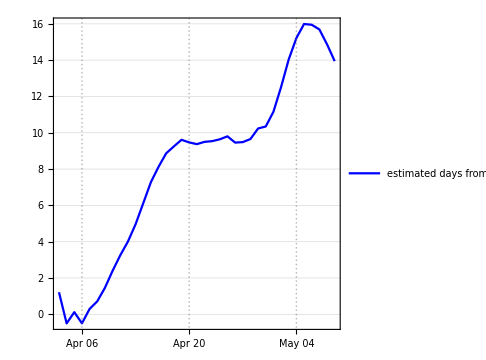

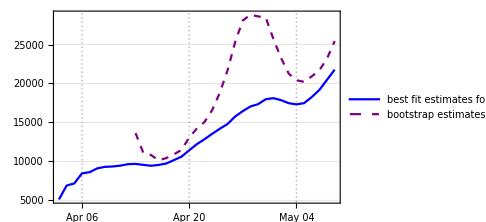

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs2[jdp0,jp20,justtime,justdata,jstartdate,21,14,0,10,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```